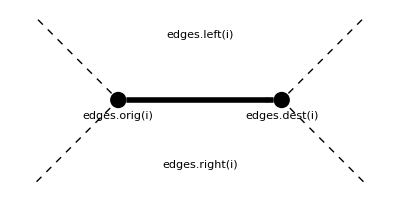

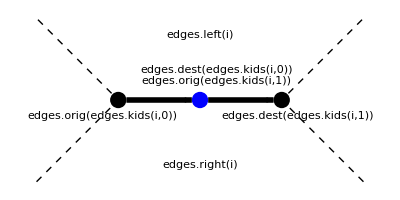

```mathematica
diskr = 0.05;
arrows = 0.05;
arrowt = 0.01;
ety = -0.1;
o = Graphics[Disk[{0,0},diskr]];
oo = Graphics[{Dashed, Line[{{-0.5,-0.5},{0,0},{-0.5,0.5}}]}];
od = Graphics[{Dashed, Line[{{1.5,-0.5},{1,0},{1.5,0.5}}]}];
d = Graphics[Disk[{1,0},diskr]];
p = Graphics[{Thickness[arrowt],Arrowheads[Large],Arrow[{{0,0},{1,0}},arrows]}];
ot = Graphics[Text[Style["edges.orig(i)",Large],{0,ety}]];
dt = Graphics[Text[Style["edges.dest(i)",Large],{1,ety}]];
lt = Graphics[Text[Style["edges.left(i)",Large],{0.5, 0.4}]];
rt = Graphics[Text[Style["edges.right(i)",Large],{0.5,-0.4}]];
nv = Graphics[{Blue,Disk[{0.5,0},diskr]}];
k0 = Graphics[{Thickness[arrowt],Arrowheads[Large],Arrow[{{0,0},{0.5,0}},arrows]}];
k1 = Graphics[{Thickness[arrowt],Arrowheads[Large],Arrow[{{0.5,0},{1,0}},arrows]}];
lt0 = Graphics[Text[Style["edges.left(i)",Large],{0.25, 0.4}]];
lt1 = Graphics[Text[Style["left",Large],{0.75, 0.2}]];
rt0 = Graphics[Text[Style["edges.right(i)",Large],{0.25,-0.4}]];
rt1 = Graphics[Text[Style["right",Large],{0.75,-0.35}]];
title=Graphics[Text[Style["edge i", Large], {0,0.25}]];
ko0 = Graphics[Text[Style["edges.orig(edges.kids(i,0))",Medium],{-0.1,ety}]];
kd0 = Graphics[Text[Style["edges.dest(edges.kids(i,0))\nedges.orig(edges.kids(i,1))",Medium],{0.6,0.15}]];
ko1 = Graphics[Text[Style["edges.orig(edges.kids(i,1))",Medium],{0.6,-ety}]];
kd1 = Graphics[Text[Style["edges.dest(edges.kids(i,1))",Medium],{1.1,ety}]];
title1 = Graphics[Text[Style["edges.divide(i)", Large],{0,0.35}]];
edge = Show[o,oo,d,od,p,ot,dt,lt,rt]
div = Show[o,oo,d,od,ko0,kd0,nv,kd1,k0,k1,lt,rt]
```